```mathematica
sqrLen[v_]:=v.v
```

```mathematica
lerp[a_,b_,t_]:=a+(b-a)*t
```

```mathematica
bc[c1_,c2_,h1_,h2_,t_]:=lerp[lerp[lerp[c1,h1,t],lerp[h1,h2,t],t],lerp[lerp[h1,h2,t],lerp[h2,c2,t],t],t]
```

```mathematica
bq[c1_,c2_,h_,t_]:=lerp[lerp[c1,h,t],lerp[h,c2,t],t]
```

```mathematica
bqD1[c1_,c2_,h_,t_]=Simplify[D[bq[c1,c2,h,t],t]]
```

2 (h+c1 (-1+t)+c2 t-2 h t)

```mathematica
bc2D1[c1_,c2_,t1_,t2_,t_]=Simplify[D[bc2[c1,c2,t1,t2,t],t]]
```

bc2^(0,0,0,0,1)[c1,c2,t1,t2,t]

```mathematica
circle[p_,r_,l_]:=p+{Sin[l*2*Pi]*r,Cos[l*2*Pi]*r}
```

```mathematica
spline1C1:={1,1}
```

```mathematica
spline1C2:={1,-1}
```

```mathematica
spline1H:={3,0}
```

```mathematica
spline1R:=0.25
```

```mathematica
spline1[l_]:=bq[spline1C1,spline1C2,spline1H,l]
```

```mathematica
spline1D1[l_]:=bqD1[spline1C1,spline1C2,spline1H,l]
```

```mathematica
spline1T[l_,l2_]:=spline1[l]+spline1D1[l]*l2
```

```mathematica
spline1N[l_,l2_]:=spline1[l]+Normalize[{-spline1D1[l][[2]],spline1D1[l][[1]]}]*l2
```

```mathematica
spline1Foo[x_,l_]:={circle[spline1[x],spline1R,l],circle[spline1[x],0.02,l],spline1N[x,l*spline1R]}
```

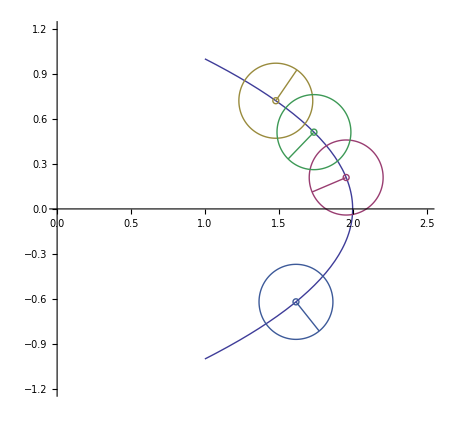

```mathematica
ParametricPlot[{spline1[l],spline1Foo[0.39534048690968804,-l],spline1Foo[0.13946715700756473,l],spline1Foo[0.24413850690707117,-l],spline1Foo[0.8096350354437104,l]},{l,0,1},PlotRange->{{0,2.5},{-1.2,1.2}},AspectRatio->Automatic]
```

```mathematica
FindRoot[qPoly1[{1,0},spline1R,spline1C1,spline1C2,spline1H,l],{l,0.8}]
```

{l→0.809635}

```mathematica
FindRoot[qPoly1[{1,0},spline1R,spline1C1,spline1C2,spline1H,l],{l,0.1}]
```

{l→0.139467}

```mathematica
FindRoot[qPoly1[{1,0},spline1R,spline1C1,spline1C2,spline1H,l],{l,0.8}]
```

{l→0.809635}

```mathematica
FindRoot[qPoly1[{1,0},spline1R,spline1C1,spline1C2,spline1H,l],{l,1}]
```

{l→0.809635}

```mathematica
evalLp2[rDir_,rP_,t_,p_]:=(t.(p-rP))/(t.rDir)
```

```mathematica
qPoly3p1[rDir_,rP_,t_,p_,r_]:=(sqrLen[p-(rP+rDir*evalLp2[rDir,rP,t,p])]-r*r)*(t.rDir)^2
```

```mathematica
qPoly3[rDir_,rP_,r_,c1_,c2_,h_,l_]:=qPoly3p1[rDir,rP,bqD1[c1,c2,h,l],bq[c1,c2,h,l],r]
```

```mathematica
evalLp1[ax_,t_,p_]:=(t.p)/(t.ax)
```

```mathematica
qPoly1p1[ax_,t_,p_,r_]:=sqrLen[p-(evalLp1[ax,t,p]*ax)]-r*r
```

```mathematica
qPoly1[ax_,r_,c1_,c2_,h_,l_]:=qPoly1p1[ax,bqD1[c1,c2,h,l],bq[c1,c2,h,l],r]
```

```mathematica
qPoly2p1[ax_,t_,p_,r_]:=((t.p))^2-2 (t.p) p[[1]] (t.ax)+(sqrLen[p]-r^2) (t.ax)^2
```

```mathematica
qPoly2[ax_,r_,c1_,c2_,h_,l_]:=qPoly2p1[ax,bqD1[c1,c2,h,l],bq[c1,c2,h,l],r]
```

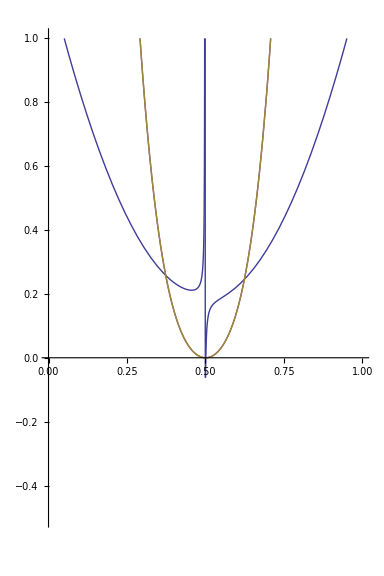

```mathematica
Plot[{qPoly1[{1,0},spline1R,spline1C1,spline1C2,spline1H,l],qPoly2[{1,0},spline1R,spline1C1,spline1C2,spline1H,l],qPoly3[{1,0},{0,0},spline1R,spline1C1,spline1C2,spline1H,l]},{l,0,1},PlotRange->{-1/2,1},AspectRatio->Automatic]
```

```mathematica
Collect[qPoly2[{1,0},spline1R,spline1C1,spline1C2,spline1H,l],l]
```

19.-140. l+396. l^2-512 l^3+256 l^4

```mathematica
Id[x_]:=x
```

```mathematica
bqP:=bq[{c1x,c1y,c1z},{c2x,c2y,c2z},{hx,hy,hz},l]
```

```mathematica
bqT:=bqD1[{c1x,c1y,c1z},{c2x,c2y,c2z},{hx,hy,hz},l]
```

```mathematica
bqTx2:=bqT[[1]]*bqT[[1]]
```

```mathematica
bqPT:=bqP.bqT
```

```mathematica
fooFunc:=-2*bqP[[1]]*bqPT*bqT[[1]]+bqPT^2+sqrLen[bqP]*bqTx2-r2*bqTx2
```

```mathematica
fooFunc2:=-2*bqP[[1]]*bqPT*bqT[[1]]+bqPT^2+sqrLen[bqP]*bqTx2-bq[rs,rt,rt,l]^2*bqTx2
```

```mathematica
Collect[Simplify[fooFunc],l]
```

4 (-20 c1x^2 c1y^2-20 c1y^4-20 c1x^2 c1z^2-40 c1y^2 c1z^2-20 c1z^4-20 c1x c1y^2 c2x-20 c1x c1z^2 c2x-4 c1y^2 c2x^2-4 c1z^2 c2x^2-8 c1x^2 c1y c2y-28 c1y^3 c2y-28 c1y c1z^2 c2y-4 c1x c1y c2x c2y-8 c1y^2 c2y^2-2 c1z^2 c2y^2-8 c1x^2 c1z c2z-28 c1y^2 c1z c2z-28 c1z^3 c2z-4 c1x c1z c2x c2z-12 c1y c1z c2y c2z-2 c1y^2 c2z^2-8 c1z^2 c2z^2+60 c1x c1y^2 hx+60 c1x c1z^2 hx+28 c1y^2 c2x hx+28 c1z^2 c2x hx+20 c1x c1y c2y hx+4 c1y c2x c2y hx+20 c1x c1z c2z hx+4 c1z c2x c2z hx-44 c1y^2 hx^2-44 c1z^2 hx^2-12 c1y c2y hx^2-12 c1z c2z hx^2+40 c1x^2 c1y hy+100 c1y^3 hy+100 c1y c1z^2 hy+32 c1x c1y c2x hy+4 c1y c2x^2 hy+4 c1x^2 c2y hy+84 c1y^2 c2y hy+26 c1z^2 c2y hy+8 c1y c2y^2 hy+58 c1y c1z c2z hy+6 c1z c2y c2z hy+2 c1y c2z^2 hy-112 c1x c1y hx hy-40 c1y c2x hx hy-8 c1x c2y hx hy+76 c1y hx^2 hy+4 c2y hx^2 hy-16 c1x^2 hy^2-172 c1y^2 hy^2-56 c1z^2 hy^2-8 c1x c2x hy^2-68 c1y c2y hy^2-24 c1z c2z hy^2+40 c1x hx hy^2+8 c2x hx hy^2-24 hx^2 hy^2+116 c1y hy^3+12 c2y hy^3-24 hy^4+40 c1x^2 c1z hz+100 c1y^2 c1z hz+100 c1z^3 hz+32 c1x c1z c2x hz+4 c1z c2x^2 hz+58 c1y c1z c2y hz+2 c1z c2y^2 hz+4 c1x^2 c2z hz+26 c1y^2 c2z hz+84 c1z^2 c2z hz+6 c1y c2y c2z hz+8 c1z c2z^2 hz-112 c1x c1z hx hz-40 c1z c2x hx hz-8 c1x c2z hx hz+76 c1z hx^2 hz+4 c2z hx^2 hz-232 c1y c1z hy hz-44 c1z c2y hy hz-44 c1y c2z hy hz+116 c1z hy^2 hz+12 c2z hy^2 hz-16 c1x^2 hz^2-56 c1y^2 hz^2-172 c1z^2 hz^2-8 c1x c2x hz^2-24 c1y c2y hz^2-68 c1z c2z hz^2+40 c1x hx hz^2+8 c2x hx hz^2-24 hx^2 hz^2+116 c1y hy hz^2+12 c2y hy hz^2-48 hy^2 hz^2+116 c1z hz^3+12 c2z hz^3-24 hz^4) l^3+4 (15 c1x^2 c1y^2+15 c1y^4+15 c1x^2 c1z^2+30 c1y^2 c1z^2+15 c1z^4+20 c1x c1y^2 c2x+20 c1x c1z^2 c2x+6 c1y^2 c2x^2+6 c1z^2 c2x^2+12 c1x^2 c1y c2y+32 c1y^3 c2y+32 c1y c1z^2 c2y+12 c1x c1y c2x c2y+2 c1y c2x^2 c2y+c1x^2 c2y^2+19 c1y^2 c2y^2+6 c1z^2 c2y^2+2 c1y c2y^3+12 c1x^2 c1z c2z+32 c1y^2 c1z c2z+32 c1z^3 c2z+12 c1x c1z c2x c2z+2 c1z c2x^2 c2z+26 c1y c1z c2y c2z+2 c1z c2y^2 c2z+c1x^2 c2z^2+6 c1y^2 c2z^2+19 c1z^2 c2z^2+2 c1y c2y c2z^2+2 c1z c2z^3-50 c1x c1y^2 hx-50 c1x c1z^2 hx-32 c1y^2 c2x hx-32 c1z^2 c2x hx-36 c1x c1y c2y hx-16 c1y c2x c2y hx-2 c1x c2y^2 hx-36 c1x c1z c2z hx-16 c1z c2x c2z hx-2 c1x c2z^2 hx+41 c1y^2 hx^2+41 c1z^2 hx^2+26 c1y c2y hx^2+c2y^2 hx^2+26 c1z c2z hx^2+c2z^2 hx^2-40 c1x^2 c1y hy-90 c1y^3 hy-90 c1y c1z^2 hy-48 c1x c1y c2x hy-12 c1y c2x^2 hy-12 c1x^2 c2y hy-128 c1y^2 c2y hy-42 c1z^2 c2y hy-8 c1x c2x c2y hy-38 c1y c2y^2 hy-86 c1y c1z c2z hy-26 c1z c2y c2z hy-12 c1y c2z^2 hy+128 c1x c1y hx hy+72 c1y c2x hx hy+32 c1x c2y hx hy+8 c2x c2y hx hy-100 c1y hx^2 hy-20 c2y hx^2 hy+24 c1x^2 hy^2+193 c1y^2 hy^2+64 c1z^2 hy^2+24 c1x c2x hy^2+4 c2x^2 hy^2+154 c1y c2y hy^2+13 c2y^2 hy^2+52 c1z c2z hy^2+4 c2z^2 hy^2-72 c1x hx hy^2-32 c2x hx hy^2+52 hx^2 hy^2-172 c1y hy^3-52 c2y hy^3+52 hy^4-40 c1x^2 c1z hz-90 c1y^2 c1z hz-90 c1z^3 hz-48 c1x c1z c2x hz-12 c1z c2x^2 hz-86 c1y c1z c2y hz-12 c1z c2y^2 hz-12 c1x^2 c2z hz-42 c1y^2 c2z hz-128 c1z^2 c2z hz-8 c1x c2x c2z hz-26 c1y c2y c2z hz-38 c1z c2z^2 hz+128 c1x c1z hx hz+72 c1z c2x hx hz+32 c1x c2z hx hz+8 c2x c2z hx hz-100 c1z hx^2 hz-20 c2z hx^2 hz+258 c1y c1z hy hz+102 c1z c2y hy hz+102 c1y c2z hy hz+18 c2y c2z hy hz-172 c1z hy^2 hz-52 c2z hy^2 hz+24 c1x^2 hz^2+64 c1y^2 hz^2+193 c1z^2 hz^2+24 c1x c2x hz^2+4 c2x^2 hz^2+52 c1y c2y hz^2+4 c2y^2 hz^2+154 c1z c2z hz^2+13 c2z^2 hz^2-72 c1x hx hz^2-32 c2x hx hz^2+52 hx^2 hz^2-172 c1y hy hz^2-52 c2y hy hz^2+104 hy^2 hz^2-172 c1z hz^3-52 c2z hz^3+52 hz^4) l^4+4 (-6 c1x^2 c1y^2-6 c1y^4-6 c1x^2 c1z^2-12 c1y^2 c1z^2-6 c1z^4-10 c1x c1y^2 c2x-10 c1x c1z^2 c2x-4 c1y^2 c2x^2-4 c1z^2 c2x^2-8 c1x^2 c1y c2y-18 c1y^3 c2y-18 c1y c1z^2 c2y-12 c1x c1y c2x c2y-4 c1y c2x^2 c2y-2 c1x^2 c2y^2-18 c1y^2 c2y^2-6 c1z^2 c2y^2-2 c1x c2x c2y^2-6 c1y c2y^3-8 c1x^2 c1z c2z-18 c1y^2 c1z c2z-18 c1z^3 c2z-12 c1x c1z c2x c2z-4 c1z c2x^2 c2z-24 c1y c1z c2y c2z-6 c1z c2y^2 c2z-2 c1x^2 c2z^2-6 c1y^2 c2z^2-18 c1z^2 c2z^2-2 c1x c2x c2z^2-6 c1y c2y c2z^2-6 c1z c2z^3+22 c1x c1y^2 hx+22 c1x c1z^2 hx+18 c1y^2 c2x hx+18 c1z^2 c2x hx+28 c1x c1y c2y hx+20 c1y c2x c2y hx+6 c1x c2y^2 hx+2 c2x c2y^2 hx+28 c1x c1z c2z hx+20 c1z c2x c2z hx+6 c1x c2z^2 hx+2 c2x c2z^2 hx-20 c1y^2 hx^2-20 c1z^2 hx^2-24 c1y c2y hx^2-4 c2y^2 hx^2-24 c1z c2z hx^2-4 c2z^2 hx^2+20 c1x^2 c1y hy+42 c1y^3 hy+42 c1y c1z^2 hy+32 c1x c1y c2x hy+12 c1y c2x^2 hy+12 c1x^2 c2y hy+90 c1y^2 c2y hy+30 c1z^2 c2y hy+16 c1x c2x c2y hy+4 c2x^2 c2y hy+54 c1y c2y^2 hy+6 c2y^3 hy+60 c1y c1z c2z hy+36 c1z c2y c2z hy+18 c1y c2z^2 hy+6 c2y c2z^2 hy-72 c1x c1y hx hy-56 c1y c2x hx hy-40 c1x c2y hx hy-24 c2x c2y hx hy+64 c1y hx^2 hy+32 c2y hx^2 hy-16 c1x^2 hy^2-108 c1y^2 hy^2-36 c1z^2 hy^2-24 c1x c2x hy^2-8 c2x^2 hy^2-144 c1y c2y hy^2-36 c2y^2 hy^2-48 c1z c2z hy^2-12 c2z^2 hy^2+56 c1x hx hy^2+40 c2x hx hy^2-48 hx^2 hy^2+120 c1y hy^3+72 c2y hy^3-48 hy^4+20 c1x^2 c1z hz+42 c1y^2 c1z hz+42 c1z^3 hz+32 c1x c1z c2x hz+12 c1z c2x^2 hz+60 c1y c1z c2y hz+18 c1z c2y^2 hz+12 c1x^2 c2z hz+30 c1y^2 c2z hz+90 c1z^2 c2z hz+16 c1x c2x c2z hz+4 c2x^2 c2z hz+36 c1y c2y c2z hz+6 c2y^2 c2z hz+54 c1z c2z^2 hz+6 c2z^3 hz-72 c1x c1z hx hz-56 c1z c2x hx hz-40 c1x c2z hx hz-24 c2x c2z hx hz+64 c1z hx^2 hz+32 c2z hx^2 hz-144 c1y c1z hy hz-96 c1z c2y hy hz-96 c1y c2z hy hz-48 c2y c2z hy hz+120 c1z hy^2 hz+72 c2z hy^2 hz-16 c1x^2 hz^2-36 c1y^2 hz^2-108 c1z^2 hz^2-24 c1x c2x hz^2-8 c2x^2 hz^2-48 c1y c2y hz^2-12 c2y^2 hz^2-144 c1z c2z hz^2-36 c2z^2 hz^2+56 c1x hx hz^2+40 c2x hx hz^2-48 hx^2 hz^2+120 c1y hy hz^2+72 c2y hy hz^2-96 hy^2 hz^2+120 c1z hz^3+72 c2z hz^3-48 hz^4) l^5+4 (c1x^2 c1y^2+c1y^4+c1x^2 c1z^2+2 c1y^2 c1z^2+c1z^4+2 c1x c1y^2 c2x+2 c1x c1z^2 c2x+c1y^2 c2x^2+c1z^2 c2x^2+2 c1x^2 c1y c2y+4 c1y^3 c2y+4 c1y c1z^2 c2y+4 c1x c1y c2x c2y+2 c1y c2x^2 c2y+c1x^2 c2y^2+6 c1y^2 c2y^2+2 c1z^2 c2y^2+2 c1x c2x c2y^2+c2x^2 c2y^2+4 c1y c2y^3+c2y^4+2 c1x^2 c1z c2z+4 c1y^2 c1z c2z+4 c1z^3 c2z+4 c1x c1z c2x c2z+2 c1z c2x^2 c2z+8 c1y c1z c2y c2z+4 c1z c2y^2 c2z+c1x^2 c2z^2+2 c1y^2 c2z^2+6 c1z^2 c2z^2+2 c1x c2x c2z^2+c2x^2 c2z^2+4 c1y c2y c2z^2+2 c2y^2 c2z^2+4 c1z c2z^3+c2z^4-4 c1x c1y^2 hx-4 c1x c1z^2 hx-4 c1y^2 c2x hx-4 c1z^2 c2x hx-8 c1x c1y c2y hx-8 c1y c2x c2y hx-4 c1x c2y^2 hx-4 c2x c2y^2 hx-8 c1x c1z c2z hx-8 c1z c2x c2z hx-4 c1x c2z^2 hx-4 c2x c2z^2 hx+4 c1y^2 hx^2+4 c1z^2 hx^2+8 c1y c2y hx^2+4 c2y^2 hx^2+8 c1z c2z hx^2+4 c2z^2 hx^2-4 c1x^2 c1y hy-8 c1y^3 hy-8 c1y c1z^2 hy-8 c1x c1y c2x hy-4 c1y c2x^2 hy-4 c1x^2 c2y hy-24 c1y^2 c2y hy-8 c1z^2 c2y hy-8 c1x c2x c2y hy-4 c2x^2 c2y hy-24 c1y c2y^2 hy-8 c2y^3 hy-16 c1y c1z c2z hy-16 c1z c2y c2z hy-8 c1y c2z^2 hy-8 c2y c2z^2 hy+16 c1x c1y hx hy+16 c1y c2x hx hy+16 c1x c2y hx hy+16 c2x c2y hx hy-16 c1y hx^2 hy-16 c2y hx^2 hy+4 c1x^2 hy^2+24 c1y^2 hy^2+8 c1z^2 hy^2+8 c1x c2x hy^2+4 c2x^2 hy^2+48 c1y c2y hy^2+24 c2y^2 hy^2+16 c1z c2z hy^2+8 c2z^2 hy^2-16 c1x hx hy^2-16 c2x hx hy^2+16 hx^2 hy^2-32 c1y hy^3-32 c2y hy^3+16 hy^4-4 c1x^2 c1z hz-8 c1y^2 c1z hz-8 c1z^3 hz-8 c1x c1z c2x hz-4 c1z c2x^2 hz-16 c1y c1z c2y hz-8 c1z c2y^2 hz-4 c1x^2 c2z hz-8 c1y^2 c2z hz-24 c1z^2 c2z hz-8 c1x c2x c2z hz-4 c2x^2 c2z hz-16 c1y c2y c2z hz-8 c2y^2 c2z hz-24 c1z c2z^2 hz-8 c2z^3 hz+16 c1x c1z hx hz+16 c1z c2x hx hz+16 c1x c2z hx hz+16 c2x c2z hx hz-16 c1z hx^2 hz-16 c2z hx^2 hz+32 c1y c1z hy hz+32 c1z c2y hy hz+32 c1y c2z hy hz+32 c2y c2z hy hz-32 c1z hy^2 hz-32 c2z hy^2 hz+4 c1x^2 hz^2+8 c1y^2 hz^2+24 c1z^2 hz^2+8 c1x c2x hz^2+4 c2x^2 hz^2+16 c1y c2y hz^2+8 c2y^2 hz^2+48 c1z c2z hz^2+24 c2z^2 hz^2-16 c1x hx hz^2-16 c2x hx hz^2+16 hx^2 hz^2-32 c1y hy hz^2-32 c2y hy hz^2+32 hy^2 hz^2-32 c1z hz^3-32 c2z hz^3+16 hz^4) l^6+4 l^2 (15 c1x^2 c1y^2+15 c1y^4+15 c1x^2 c1z^2+30 c1y^2 c1z^2+15 c1z^4+10 c1x c1y^2 c2x+10 c1x c1z^2 c2x+c1y^2 c2x^2+c1z^2 c2x^2+2 c1x^2 c1y c2y+12 c1y^3 c2y+12 c1y c1z^2 c2y+c1y^2 c2y^2+2 c1x^2 c1z c2z+12 c1y^2 c1z c2z+12 c1z^3 c2z+2 c1y c1z c2y c2z+c1z^2 c2z^2-40 c1x c1y^2 hx-40 c1x c1z^2 hx-12 c1y^2 c2x hx-12 c1z^2 c2x hx-4 c1x c1y c2y hx-4 c1x c1z c2z hx+26 c1y^2 hx^2+26 c1z^2 hx^2+2 c1y c2y hx^2+2 c1z c2z hx^2-20 c1x^2 c1y hy-60 c1y^3 hy-60 c1y c1z^2 hy-8 c1x c1y c2x hy-24 c1y^2 c2y hy-6 c1z^2 c2y hy-18 c1y c1z c2z hy+48 c1x c1y hx hy+8 c1y c2x hx hy-28 c1y hx^2 hy+4 c1x^2 hy^2+78 c1y^2 hy^2+24 c1z^2 hy^2+10 c1y c2y hy^2+4 c1z c2z hy^2-8 c1x hx hy^2+4 hx^2 hy^2-36 c1y hy^3+4 hy^4-20 c1x^2 c1z hz-60 c1y^2 c1z hz-60 c1z^3 hz-8 c1x c1z c2x hz-18 c1y c1z c2y hz-6 c1y^2 c2z hz-24 c1z^2 c2z hz+48 c1x c1z hx hz+8 c1z c2x hx hz-28 c1z hx^2 hz+108 c1y c1z hy hz+6 c1z c2y hy hz+6 c1y c2z hy hz-36 c1z hy^2 hz+4 c1x^2 hz^2+24 c1y^2 hz^2+78 c1z^2 hz^2+4 c1y c2y hz^2+10 c1z c2z hz^2-8 c1x hx hz^2+4 hx^2 hz^2-36 c1y hy hz^2+8 hy^2 hz^2-36 c1z hz^3+4 hz^4-c1x^2 r2-2 c1x c2x r2-c2x^2 r2+4 c1x hx r2+4 c2x hx r2-4 hx^2 r2)+4 (c1x^2 c1y^2+c1y^4+c1x^2 c1z^2+2 c1y^2 c1z^2+c1z^4-2 c1x c1y^2 hx-2 c1x c1z^2 hx+c1y^2 hx^2+c1z^2 hx^2-2 c1y^3 hy-2 c1y c1z^2 hy+c1y^2 hy^2-2 c1y^2 c1z hz-2 c1z^3 hz+2 c1y c1z hy hz+c1z^2 hz^2-c1x^2 r2+2 c1x hx r2-hx^2 r2)+4 l (-6 c1x^2 c1y^2-6 c1y^4-6 c1x^2 c1z^2-12 c1y^2 c1z^2-6 c1z^4-2 c1x c1y^2 c2x-2 c1x c1z^2 c2x-2 c1y^3 c2y-2 c1y c1z^2 c2y-2 c1y^2 c1z c2z-2 c1z^3 c2z+14 c1x c1y^2 hx+14 c1x c1z^2 hx+2 c1y^2 c2x hx+2 c1z^2 c2x hx-8 c1y^2 hx^2-8 c1z^2 hx^2+4 c1x^2 c1y hy+18 c1y^3 hy+18 c1y c1z^2 hy+2 c1y^2 c2y hy+2 c1y c1z c2z hy-8 c1x c1y hx hy+4 c1y hx^2 hy-16 c1y^2 hy^2-4 c1z^2 hy^2+4 c1y hy^3+4 c1x^2 c1z hz+18 c1y^2 c1z hz+18 c1z^3 hz+2 c1y c1z c2y hz+2 c1z^2 c2z hz-8 c1x c1z hx hz+4 c1z hx^2 hz-24 c1y c1z hy hz+4 c1z hy^2 hz-4 c1y^2 hz^2-16 c1z^2 hz^2+4 c1y hy hz^2+4 c1z hz^3+2 c1x^2 r2+2 c1x c2x r2-6 c1x hx r2-2 c2x hx r2+4 hx^2 r2)

```mathematica
Simplify[c1x^2 c1y^2+c1y^4+c1x^2 c1z^2+2 c1y^2 c1z^2+c1z^4+2 c1x c1y^2 c2x+2 c1x c1z^2 c2x+c1y^2 c2x^2+c1z^2 c2x^2+2 c1x^2 c1y c2y+4 c1y^3 c2y+4 c1y c1z^2 c2y+4 c1x c1y c2x c2y+2 c1y c2x^2 c2y+c1x^2 c2y^2+6 c1y^2 c2y^2+2 c1z^2 c2y^2+2 c1x c2x c2y^2+c2x^2 c2y^2+4 c1y c2y^3+c2y^4+2 c1x^2 c1z c2z+4 c1y^2 c1z c2z+4 c1z^3 c2z+4 c1x c1z c2x c2z+2 c1z c2x^2 c2z+8 c1y c1z c2y c2z+4 c1z c2y^2 c2z+c1x^2 c2z^2+2 c1y^2 c2z^2+6 c1z^2 c2z^2+2 c1x c2x c2z^2+c2x^2 c2z^2+4 c1y c2y c2z^2+2 c2y^2 c2z^2+4 c1z c2z^3+c2z^4-4 c1x c1y^2 hx-4 c1x c1z^2 hx-4 c1y^2 c2x hx-4 c1z^2 c2x hx-8 c1x c1y c2y hx-8 c1y c2x c2y hx-4 c1x c2y^2 hx-4 c2x c2y^2 hx-8 c1x c1z c2z hx-8 c1z c2x c2z hx-4 c1x c2z^2 hx-4 c2x c2z^2 hx+4 c1y^2 hx^2+4 c1z^2 hx^2+8 c1y c2y hx^2+4 c2y^2 hx^2+8 c1z c2z hx^2+4 c2z^2 hx^2-4 c1x^2 c1y hy-8 c1y^3 hy-8 c1y c1z^2 hy-8 c1x c1y c2x hy-4 c1y c2x^2 hy-4 c1x^2 c2y hy-24 c1y^2 c2y hy-8 c1z^2 c2y hy-8 c1x c2x c2y hy-4 c2x^2 c2y hy-24 c1y c2y^2 hy-8 c2y^3 hy-16 c1y c1z c2z hy-16 c1z c2y c2z hy-8 c1y c2z^2 hy-8 c2y c2z^2 hy+16 c1x c1y hx hy+16 c1y c2x hx hy+16 c1x c2y hx hy+16 c2x c2y hx hy-16 c1y hx^2 hy-16 c2y hx^2 hy+4 c1x^2 hy^2+24 c1y^2 hy^2+8 c1z^2 hy^2+8 c1x c2x hy^2+4 c2x^2 hy^2+48 c1y c2y hy^2+24 c2y^2 hy^2+16 c1z c2z hy^2+8 c2z^2 hy^2-16 c1x hx hy^2-16 c2x hx hy^2+16 hx^2 hy^2-32 c1y hy^3-32 c2y hy^3+16 hy^4-4 c1x^2 c1z hz-8 c1y^2 c1z hz-8 c1z^3 hz-8 c1x c1z c2x hz-4 c1z c2x^2 hz-16 c1y c1z c2y hz-8 c1z c2y^2 hz-4 c1x^2 c2z hz-8 c1y^2 c2z hz-24 c1z^2 c2z hz-8 c1x c2x c2z hz-4 c2x^2 c2z hz-16 c1y c2y c2z hz-8 c2y^2 c2z hz-24 c1z c2z^2 hz-8 c2z^3 hz+16 c1x c1z hx hz+16 c1z c2x hx hz+16 c1x c2z hx hz+16 c2x c2z hx hz-16 c1z hx^2 hz-16 c2z hx^2 hz+32 c1y c1z hy hz+32 c1z c2y hy hz+32 c1y c2z hy hz+32 c2y c2z hy hz-32 c1z hy^2 hz-32 c2z hy^2 hz+4 c1x^2 hz^2+8 c1y^2 hz^2+24 c1z^2 hz^2+8 c1x c2x hz^2+4 c2x^2 hz^2+16 c1y c2y hz^2+8 c2y^2 hz^2+48 c1z c2z hz^2+24 c2z^2 hz^2-16 c1x hx hz^2-16 c2x hx hz^2+16 hx^2 hz^2-32 c1y hy hz^2-32 c2y hy hz^2+32 hy^2 hz^2-32 c1z hz^3-32 c2z hz^3+16 hz^4]
```

(c1y^2+c1z^2+c2y^2+c2z^2+2 c1y (c2y-2 hy)-4 c2y hy+4 hy^2+2 c1z (c2z-2 hz)-4 c2z hz+4 hz^2) (c1x^2+c1y^2+c1z^2+c2x^2+c2y^2+2 c1z c2z+c2z^2+2 c1x (c2x-2 hx)-4 c2x hx+4 hx^2+2 c1y (c2y-2 hy)-4 c2y hy+4 hy^2-4 c1z hz-4 c2z hz+4 hz^2)

```mathematica
Simplify[-20 c1x^2 c1y^2-20 c1y^4-20 c1x^2 c1z^2-40 c1y^2 c1z^2-20 c1z^4-20 c1x c1y^2 c2x-20 c1x c1z^2 c2x-4 c1y^2 c2x^2-4 c1z^2 c2x^2-8 c1x^2 c1y c2y-28 c1y^3 c2y-28 c1y c1z^2 c2y-4 c1x c1y c2x c2y-8 c1y^2 c2y^2-2 c1z^2 c2y^2-8 c1x^2 c1z c2z-28 c1y^2 c1z c2z-28 c1z^3 c2z-4 c1x c1z c2x c2z-12 c1y c1z c2y c2z-2 c1y^2 c2z^2-8 c1z^2 c2z^2+60 c1x c1y^2 hx+60 c1x c1z^2 hx+28 c1y^2 c2x hx+28 c1z^2 c2x hx+20 c1x c1y c2y hx+4 c1y c2x c2y hx+20 c1x c1z c2z hx+4 c1z c2x c2z hx-44 c1y^2 hx^2-44 c1z^2 hx^2-12 c1y c2y hx^2-12 c1z c2z hx^2+40 c1x^2 c1y hy+100 c1y^3 hy+100 c1y c1z^2 hy+32 c1x c1y c2x hy+4 c1y c2x^2 hy+4 c1x^2 c2y hy+84 c1y^2 c2y hy+26 c1z^2 c2y hy+8 c1y c2y^2 hy+58 c1y c1z c2z hy+6 c1z c2y c2z hy+2 c1y c2z^2 hy-112 c1x c1y hx hy-40 c1y c2x hx hy-8 c1x c2y hx hy+76 c1y hx^2 hy+4 c2y hx^2 hy-16 c1x^2 hy^2-172 c1y^2 hy^2-56 c1z^2 hy^2-8 c1x c2x hy^2-68 c1y c2y hy^2-24 c1z c2z hy^2+40 c1x hx hy^2+8 c2x hx hy^2-24 hx^2 hy^2+116 c1y hy^3+12 c2y hy^3-24 hy^4+40 c1x^2 c1z hz+100 c1y^2 c1z hz+100 c1z^3 hz+32 c1x c1z c2x hz+4 c1z c2x^2 hz+58 c1y c1z c2y hz+2 c1z c2y^2 hz+4 c1x^2 c2z hz+26 c1y^2 c2z hz+84 c1z^2 c2z hz+6 c1y c2y c2z hz+8 c1z c2z^2 hz-112 c1x c1z hx hz-40 c1z c2x hx hz-8 c1x c2z hx hz+76 c1z hx^2 hz+4 c2z hx^2 hz-232 c1y c1z hy hz-44 c1z c2y hy hz-44 c1y c2z hy hz+116 c1z hy^2 hz+12 c2z hy^2 hz-16 c1x^2 hz^2-56 c1y^2 hz^2-172 c1z^2 hz^2-8 c1x c2x hz^2-24 c1y c2y hz^2-68 c1z c2z hz^2+40 c1x hx hz^2+8 c2x hx hz^2-24 hx^2 hz^2+116 c1y hy hz^2+12 c2y hy hz^2-48 hy^2 hz^2+116 c1z hz^3+12 c2z hz^3-24 hz^4]
```

-2 (10 c1y^4+10 c1z^4+2 c1z^2 c2x^2+c1z^2 c2y^2+14 c1z^3 c2z+4 c1z^2 c2z^2-14 c1z^2 c2x hx-2 c1z c2x c2z hx+22 c1z^2 hx^2+6 c1z c2z hx^2+2 c1y^3 (7 c2y-25 hy)-13 c1z^2 c2y hy-3 c1z c2y c2z hy-2 c2y hx^2 hy+28 c1z^2 hy^2+12 c1z c2z hy^2-4 c2x hx hy^2+12 hx^2 hy^2-6 c2y hy^3+12 hy^4-50 c1z^3 hz-2 c1z c2x^2 hz-c1z c2y^2 hz-42 c1z^2 c2z hz-4 c1z c2z^2 hz+20 c1z c2x hx hz-38 c1z hx^2 hz-2 c2z hx^2 hz+22 c1z c2y hy hz-58 c1z hy^2 hz-6 c2z hy^2 hz+86 c1z^2 hz^2+34 c1z c2z hz^2-4 c2x hx hz^2+12 hx^2 hz^2-6 c2y hy hz^2+24 hy^2 hz^2-58 c1z hz^3-6 c2z hz^3+12 hz^4+2 c1x^2 (5 c1y^2+5 c1z^2+2 c1y (c2y-5 hy)-c2y hy+4 hy^2+2 c1z (c2z-5 hz)-c2z hz+4 hz^2)+c1y^2 (20 c1z^2+2 c2x^2+4 c2y^2+14 c1z c2z+c2z^2-14 c2x hx+22 hx^2-42 c2y hy+86 hy^2-50 c1z hz-13 c2z hz+28 hz^2)-c1y (-6 c2y hx^2+2 c2x hx (c2y-10 hy)+2 c2x^2 hy+4 c2y^2 hy+c2z^2 hy+38 hx^2 hy-34 c2y hy^2+58 hy^3+c1z^2 (-14 c2y+50 hy)+3 c2y c2z hz-22 c2z hy hz-12 c2y hz^2+58 hy hz^2+c1z (29 hy (c2z-4 hz)+c2y (-6 c2z+29 hz)))+2 c1x (5 c1y^2 (c2x-3 hx)+5 c1z^2 (c2x-3 hx)+c1y (-5 c2y hx+c2x (c2y-8 hy)+28 hx hy)+c1z (-5 c2z hx+c2x (c2z-8 hz)+28 hx hz)+2 (c2y hx hy+hx (-5 hy^2+(c2z-5 hz) hz)+c2x (hy^2+hz^2))))

```mathematica
Collect[Simplify[fooFunc2],l]
```

4 (c1x^2 c1y^2+c1y^4+c1x^2 c1z^2+2 c1y^2 c1z^2+c1z^4-2 c1x c1y^2 hx-2 c1x c1z^2 hx+c1y^2 hx^2+c1z^2 hx^2-2 c1y^3 hy-2 c1y c1z^2 hy+c1y^2 hy^2-2 c1y^2 c1z hz-2 c1z^3 hz+2 c1y c1z hy hz+c1z^2 hz^2-c1x^2 rs^2+2 c1x hx rs^2-hx^2 rs^2)+4 l (-6 c1x^2 c1y^2-6 c1y^4-6 c1x^2 c1z^2-12 c1y^2 c1z^2-6 c1z^4-2 c1x c1y^2 c2x-2 c1x c1z^2 c2x-2 c1y^3 c2y-2 c1y c1z^2 c2y-2 c1y^2 c1z c2z-2 c1z^3 c2z+14 c1x c1y^2 hx+14 c1x c1z^2 hx+2 c1y^2 c2x hx+2 c1z^2 c2x hx-8 c1y^2 hx^2-8 c1z^2 hx^2+4 c1x^2 c1y hy+18 c1y^3 hy+18 c1y c1z^2 hy+2 c1y^2 c2y hy+2 c1y c1z c2z hy-8 c1x c1y hx hy+4 c1y hx^2 hy-16 c1y^2 hy^2-4 c1z^2 hy^2+4 c1y hy^3+4 c1x^2 c1z hz+18 c1y^2 c1z hz+18 c1z^3 hz+2 c1y c1z c2y hz+2 c1z^2 c2z hz-8 c1x c1z hx hz+4 c1z hx^2 hz-24 c1y c1z hy hz+4 c1z hy^2 hz-4 c1y^2 hz^2-16 c1z^2 hz^2+4 c1y hy hz^2+4 c1z hz^3+6 c1x^2 rs^2+2 c1x c2x rs^2-14 c1x hx rs^2-2 c2x hx rs^2+8 hx^2 rs^2-4 c1x^2 rs rt+8 c1x hx rs rt-4 hx^2 rs rt)+4 l^4 (15 c1x^2 c1y^2+15 c1y^4+15 c1x^2 c1z^2+30 c1y^2 c1z^2+15 c1z^4+20 c1x c1y^2 c2x+20 c1x c1z^2 c2x+6 c1y^2 c2x^2+6 c1z^2 c2x^2+12 c1x^2 c1y c2y+32 c1y^3 c2y+32 c1y c1z^2 c2y+12 c1x c1y c2x c2y+2 c1y c2x^2 c2y+c1x^2 c2y^2+19 c1y^2 c2y^2+6 c1z^2 c2y^2+2 c1y c2y^3+12 c1x^2 c1z c2z+32 c1y^2 c1z c2z+32 c1z^3 c2z+12 c1x c1z c2x c2z+2 c1z c2x^2 c2z+26 c1y c1z c2y c2z+2 c1z c2y^2 c2z+c1x^2 c2z^2+6 c1y^2 c2z^2+19 c1z^2 c2z^2+2 c1y c2y c2z^2+2 c1z c2z^3-50 c1x c1y^2 hx-50 c1x c1z^2 hx-32 c1y^2 c2x hx-32 c1z^2 c2x hx-36 c1x c1y c2y hx-16 c1y c2x c2y hx-2 c1x c2y^2 hx-36 c1x c1z c2z hx-16 c1z c2x c2z hx-2 c1x c2z^2 hx+41 c1y^2 hx^2+41 c1z^2 hx^2+26 c1y c2y hx^2+c2y^2 hx^2+26 c1z c2z hx^2+c2z^2 hx^2-40 c1x^2 c1y hy-90 c1y^3 hy-90 c1y c1z^2 hy-48 c1x c1y c2x hy-12 c1y c2x^2 hy-12 c1x^2 c2y hy-128 c1y^2 c2y hy-42 c1z^2 c2y hy-8 c1x c2x c2y hy-38 c1y c2y^2 hy-86 c1y c1z c2z hy-26 c1z c2y c2z hy-12 c1y c2z^2 hy+128 c1x c1y hx hy+72 c1y c2x hx hy+32 c1x c2y hx hy+8 c2x c2y hx hy-100 c1y hx^2 hy-20 c2y hx^2 hy+24 c1x^2 hy^2+193 c1y^2 hy^2+64 c1z^2 hy^2+24 c1x c2x hy^2+4 c2x^2 hy^2+154 c1y c2y hy^2+13 c2y^2 hy^2+52 c1z c2z hy^2+4 c2z^2 hy^2-72 c1x hx hy^2-32 c2x hx hy^2+52 hx^2 hy^2-172 c1y hy^3-52 c2y hy^3+52 hy^4-40 c1x^2 c1z hz-90 c1y^2 c1z hz-90 c1z^3 hz-48 c1x c1z c2x hz-12 c1z c2x^2 hz-86 c1y c1z c2y hz-12 c1z c2y^2 hz-12 c1x^2 c2z hz-42 c1y^2 c2z hz-128 c1z^2 c2z hz-8 c1x c2x c2z hz-26 c1y c2y c2z hz-38 c1z c2z^2 hz+128 c1x c1z hx hz+72 c1z c2x hx hz+32 c1x c2z hx hz+8 c2x c2z hx hz-100 c1z hx^2 hz-20 c2z hx^2 hz+258 c1y c1z hy hz+102 c1z c2y hy hz+102 c1y c2z hy hz+18 c2y c2z hy hz-172 c1z hy^2 hz-52 c2z hy^2 hz+24 c1x^2 hz^2+64 c1y^2 hz^2+193 c1z^2 hz^2+24 c1x c2x hz^2+4 c2x^2 hz^2+52 c1y c2y hz^2+4 c2y^2 hz^2+154 c1z c2z hz^2+13 c2z^2 hz^2-72 c1x hx hz^2-32 c2x hx hz^2+52 hx^2 hz^2-172 c1y hy hz^2-52 c2y hy hz^2+104 hy^2 hz^2-172 c1z hz^3-52 c2z hz^3+52 hz^4-15 c1x^2 rs^2-20 c1x c2x rs^2-6 c2x^2 rs^2+50 c1x hx rs^2+32 c2x hx rs^2-41 hx^2 rs^2+28 c1x^2 rs rt+36 c1x c2x rs rt+10 c2x^2 rs rt-92 c1x hx rs rt-56 c2x hx rs rt+74 hx^2 rs rt-13 c1x^2 rt^2-16 c1x c2x rt^2-4 c2x^2 rt^2+42 c1x hx rt^2+24 c2x hx rt^2-33 hx^2 rt^2)+4 l^2 (15 c1x^2 c1y^2+15 c1y^4+15 c1x^2 c1z^2+30 c1y^2 c1z^2+15 c1z^4+10 c1x c1y^2 c2x+10 c1x c1z^2 c2x+c1y^2 c2x^2+c1z^2 c2x^2+2 c1x^2 c1y c2y+12 c1y^3 c2y+12 c1y c1z^2 c2y+c1y^2 c2y^2+2 c1x^2 c1z c2z+12 c1y^2 c1z c2z+12 c1z^3 c2z+2 c1y c1z c2y c2z+c1z^2 c2z^2-40 c1x c1y^2 hx-40 c1x c1z^2 hx-12 c1y^2 c2x hx-12 c1z^2 c2x hx-4 c1x c1y c2y hx-4 c1x c1z c2z hx+26 c1y^2 hx^2+26 c1z^2 hx^2+2 c1y c2y hx^2+2 c1z c2z hx^2-20 c1x^2 c1y hy-60 c1y^3 hy-60 c1y c1z^2 hy-8 c1x c1y c2x hy-24 c1y^2 c2y hy-6 c1z^2 c2y hy-18 c1y c1z c2z hy+48 c1x c1y hx hy+8 c1y c2x hx hy-28 c1y hx^2 hy+4 c1x^2 hy^2+78 c1y^2 hy^2+24 c1z^2 hy^2+10 c1y c2y hy^2+4 c1z c2z hy^2-8 c1x hx hy^2+4 hx^2 hy^2-36 c1y hy^3+4 hy^4-20 c1x^2 c1z hz-60 c1y^2 c1z hz-60 c1z^3 hz-8 c1x c1z c2x hz-18 c1y c1z c2y hz-6 c1y^2 c2z hz-24 c1z^2 c2z hz+48 c1x c1z hx hz+8 c1z c2x hx hz-28 c1z hx^2 hz+108 c1y c1z hy hz+6 c1z c2y hy hz+6 c1y c2z hy hz-36 c1z hy^2 hz+4 c1x^2 hz^2+24 c1y^2 hz^2+78 c1z^2 hz^2+4 c1y c2y hz^2+10 c1z c2z hz^2-8 c1x hx hz^2+4 hx^2 hz^2-36 c1y hy hz^2+8 hy^2 hz^2-36 c1z hz^3+4 hz^4-15 c1x^2 rs^2-10 c1x c2x rs^2-c2x^2 rs^2+40 c1x hx rs^2+12 c2x hx rs^2-26 hx^2 rs^2+18 c1x^2 rs rt+8 c1x c2x rs rt-44 c1x hx rs rt-8 c2x hx rs rt+26 hx^2 rs rt-4 c1x^2 rt^2+8 c1x hx rt^2-4 hx^2 rt^2)+4 l^6 (c1x^2 c1y^2+c1y^4+c1x^2 c1z^2+2 c1y^2 c1z^2+c1z^4+2 c1x c1y^2 c2x+2 c1x c1z^2 c2x+c1y^2 c2x^2+c1z^2 c2x^2+2 c1x^2 c1y c2y+4 c1y^3 c2y+4 c1y c1z^2 c2y+4 c1x c1y c2x c2y+2 c1y c2x^2 c2y+c1x^2 c2y^2+6 c1y^2 c2y^2+2 c1z^2 c2y^2+2 c1x c2x c2y^2+c2x^2 c2y^2+4 c1y c2y^3+c2y^4+2 c1x^2 c1z c2z+4 c1y^2 c1z c2z+4 c1z^3 c2z+4 c1x c1z c2x c2z+2 c1z c2x^2 c2z+8 c1y c1z c2y c2z+4 c1z c2y^2 c2z+c1x^2 c2z^2+2 c1y^2 c2z^2+6 c1z^2 c2z^2+2 c1x c2x c2z^2+c2x^2 c2z^2+4 c1y c2y c2z^2+2 c2y^2 c2z^2+4 c1z c2z^3+c2z^4-4 c1x c1y^2 hx-4 c1x c1z^2 hx-4 c1y^2 c2x hx-4 c1z^2 c2x hx-8 c1x c1y c2y hx-8 c1y c2x c2y hx-4 c1x c2y^2 hx-4 c2x c2y^2 hx-8 c1x c1z c2z hx-8 c1z c2x c2z hx-4 c1x c2z^2 hx-4 c2x c2z^2 hx+4 c1y^2 hx^2+4 c1z^2 hx^2+8 c1y c2y hx^2+4 c2y^2 hx^2+8 c1z c2z hx^2+4 c2z^2 hx^2-4 c1x^2 c1y hy-8 c1y^3 hy-8 c1y c1z^2 hy-8 c1x c1y c2x hy-4 c1y c2x^2 hy-4 c1x^2 c2y hy-24 c1y^2 c2y hy-8 c1z^2 c2y hy-8 c1x c2x c2y hy-4 c2x^2 c2y hy-24 c1y c2y^2 hy-8 c2y^3 hy-16 c1y c1z c2z hy-16 c1z c2y c2z hy-8 c1y c2z^2 hy-8 c2y c2z^2 hy+16 c1x c1y hx hy+16 c1y c2x hx hy+16 c1x c2y hx hy+16 c2x c2y hx hy-16 c1y hx^2 hy-16 c2y hx^2 hy+4 c1x^2 hy^2+24 c1y^2 hy^2+8 c1z^2 hy^2+8 c1x c2x hy^2+4 c2x^2 hy^2+48 c1y c2y hy^2+24 c2y^2 hy^2+16 c1z c2z hy^2+8 c2z^2 hy^2-16 c1x hx hy^2-16 c2x hx hy^2+16 hx^2 hy^2-32 c1y hy^3-32 c2y hy^3+16 hy^4-4 c1x^2 c1z hz-8 c1y^2 c1z hz-8 c1z^3 hz-8 c1x c1z c2x hz-4 c1z c2x^2 hz-16 c1y c1z c2y hz-8 c1z c2y^2 hz-4 c1x^2 c2z hz-8 c1y^2 c2z hz-24 c1z^2 c2z hz-8 c1x c2x c2z hz-4 c2x^2 c2z hz-16 c1y c2y c2z hz-8 c2y^2 c2z hz-24 c1z c2z^2 hz-8 c2z^3 hz+16 c1x c1z hx hz+16 c1z c2x hx hz+16 c1x c2z hx hz+16 c2x c2z hx hz-16 c1z hx^2 hz-16 c2z hx^2 hz+32 c1y c1z hy hz+32 c1z c2y hy hz+32 c1y c2z hy hz+32 c2y c2z hy hz-32 c1z hy^2 hz-32 c2z hy^2 hz+4 c1x^2 hz^2+8 c1y^2 hz^2+24 c1z^2 hz^2+8 c1x c2x hz^2+4 c2x^2 hz^2+16 c1y c2y hz^2+8 c2y^2 hz^2+48 c1z c2z hz^2+24 c2z^2 hz^2-16 c1x hx hz^2-16 c2x hx hz^2+16 hx^2 hz^2-32 c1y hy hz^2-32 c2y hy hz^2+32 hy^2 hz^2-32 c1z hz^3-32 c2z hz^3+16 hz^4-c1x^2 rs^2-2 c1x c2x rs^2-c2x^2 rs^2+4 c1x hx rs^2+4 c2x hx rs^2-4 hx^2 rs^2+2 c1x^2 rs rt+4 c1x c2x rs rt+2 c2x^2 rs rt-8 c1x hx rs rt-8 c2x hx rs rt+8 hx^2 rs rt-c1x^2 rt^2-2 c1x c2x rt^2-c2x^2 rt^2+4 c1x hx rt^2+4 c2x hx rt^2-4 hx^2 rt^2)+4 l^5 (-6 c1x^2 c1y^2-6 c1y^4-6 c1x^2 c1z^2-12 c1y^2 c1z^2-6 c1z^4-10 c1x c1y^2 c2x-10 c1x c1z^2 c2x-4 c1y^2 c2x^2-4 c1z^2 c2x^2-8 c1x^2 c1y c2y-18 c1y^3 c2y-18 c1y c1z^2 c2y-12 c1x c1y c2x c2y-4 c1y c2x^2 c2y-2 c1x^2 c2y^2-18 c1y^2 c2y^2-6 c1z^2 c2y^2-2 c1x c2x c2y^2-6 c1y c2y^3-8 c1x^2 c1z c2z-18 c1y^2 c1z c2z-18 c1z^3 c2z-12 c1x c1z c2x c2z-4 c1z c2x^2 c2z-24 c1y c1z c2y c2z-6 c1z c2y^2 c2z-2 c1x^2 c2z^2-6 c1y^2 c2z^2-18 c1z^2 c2z^2-2 c1x c2x c2z^2-6 c1y c2y c2z^2-6 c1z c2z^3+22 c1x c1y^2 hx+22 c1x c1z^2 hx+18 c1y^2 c2x hx+18 c1z^2 c2x hx+28 c1x c1y c2y hx+20 c1y c2x c2y hx+6 c1x c2y^2 hx+2 c2x c2y^2 hx+28 c1x c1z c2z hx+20 c1z c2x c2z hx+6 c1x c2z^2 hx+2 c2x c2z^2 hx-20 c1y^2 hx^2-20 c1z^2 hx^2-24 c1y c2y hx^2-4 c2y^2 hx^2-24 c1z c2z hx^2-4 c2z^2 hx^2+20 c1x^2 c1y hy+42 c1y^3 hy+42 c1y c1z^2 hy+32 c1x c1y c2x hy+12 c1y c2x^2 hy+12 c1x^2 c2y hy+90 c1y^2 c2y hy+30 c1z^2 c2y hy+16 c1x c2x c2y hy+4 c2x^2 c2y hy+54 c1y c2y^2 hy+6 c2y^3 hy+60 c1y c1z c2z hy+36 c1z c2y c2z hy+18 c1y c2z^2 hy+6 c2y c2z^2 hy-72 c1x c1y hx hy-56 c1y c2x hx hy-40 c1x c2y hx hy-24 c2x c2y hx hy+64 c1y hx^2 hy+32 c2y hx^2 hy-16 c1x^2 hy^2-108 c1y^2 hy^2-36 c1z^2 hy^2-24 c1x c2x hy^2-8 c2x^2 hy^2-144 c1y c2y hy^2-36 c2y^2 hy^2-48 c1z c2z hy^2-12 c2z^2 hy^2+56 c1x hx hy^2+40 c2x hx hy^2-48 hx^2 hy^2+120 c1y hy^3+72 c2y hy^3-48 hy^4+20 c1x^2 c1z hz+42 c1y^2 c1z hz+42 c1z^3 hz+32 c1x c1z c2x hz+12 c1z c2x^2 hz+60 c1y c1z c2y hz+18 c1z c2y^2 hz+12 c1x^2 c2z hz+30 c1y^2 c2z hz+90 c1z^2 c2z hz+16 c1x c2x c2z hz+4 c2x^2 c2z hz+36 c1y c2y c2z hz+6 c2y^2 c2z hz+54 c1z c2z^2 hz+6 c2z^3 hz-72 c1x c1z hx hz-56 c1z c2x hx hz-40 c1x c2z hx hz-24 c2x c2z hx hz+64 c1z hx^2 hz+32 c2z hx^2 hz-144 c1y c1z hy hz-96 c1z c2y hy hz-96 c1y c2z hy hz-48 c2y c2z hy hz+120 c1z hy^2 hz+72 c2z hy^2 hz-16 c1x^2 hz^2-36 c1y^2 hz^2-108 c1z^2 hz^2-24 c1x c2x hz^2-8 c2x^2 hz^2-48 c1y c2y hz^2-12 c2y^2 hz^2-144 c1z c2z hz^2-36 c2z^2 hz^2+56 c1x hx hz^2+40 c2x hx hz^2-48 hx^2 hz^2+120 c1y hy hz^2+72 c2y hy hz^2-96 hy^2 hz^2+120 c1z hz^3+72 c2z hz^3-48 hz^4+6 c1x^2 rs^2+10 c1x c2x rs^2+4 c2x^2 rs^2-22 c1x hx rs^2-18 c2x hx rs^2+20 hx^2 rs^2-12 c1x^2 rs rt-20 c1x c2x rs rt-8 c2x^2 rs rt+44 c1x hx rs rt+36 c2x hx rs rt-40 hx^2 rs rt+6 c1x^2 rt^2+10 c1x c2x rt^2+4 c2x^2 rt^2-22 c1x hx rt^2-18 c2x hx rt^2+20 hx^2 rt^2)+4 l^3 (-20 c1x^2 c1y^2-20 c1y^4-20 c1x^2 c1z^2-40 c1y^2 c1z^2-20 c1z^4-20 c1x c1y^2 c2x-20 c1x c1z^2 c2x-4 c1y^2 c2x^2-4 c1z^2 c2x^2-8 c1x^2 c1y c2y-28 c1y^3 c2y-28 c1y c1z^2 c2y-4 c1x c1y c2x c2y-8 c1y^2 c2y^2-2 c1z^2 c2y^2-8 c1x^2 c1z c2z-28 c1y^2 c1z c2z-28 c1z^3 c2z-4 c1x c1z c2x c2z-12 c1y c1z c2y c2z-2 c1y^2 c2z^2-8 c1z^2 c2z^2+60 c1x c1y^2 hx+60 c1x c1z^2 hx+28 c1y^2 c2x hx+28 c1z^2 c2x hx+20 c1x c1y c2y hx+4 c1y c2x c2y hx+20 c1x c1z c2z hx+4 c1z c2x c2z hx-44 c1y^2 hx^2-44 c1z^2 hx^2-12 c1y c2y hx^2-12 c1z c2z hx^2+40 c1x^2 c1y hy+100 c1y^3 hy+100 c1y c1z^2 hy+32 c1x c1y c2x hy+4 c1y c2x^2 hy+4 c1x^2 c2y hy+84 c1y^2 c2y hy+26 c1z^2 c2y hy+8 c1y c2y^2 hy+58 c1y c1z c2z hy+6 c1z c2y c2z hy+2 c1y c2z^2 hy-112 c1x c1y hx hy-40 c1y c2x hx hy-8 c1x c2y hx hy+76 c1y hx^2 hy+4 c2y hx^2 hy-16 c1x^2 hy^2-172 c1y^2 hy^2-56 c1z^2 hy^2-8 c1x c2x hy^2-68 c1y c2y hy^2-24 c1z c2z hy^2+40 c1x hx hy^2+8 c2x hx hy^2-24 hx^2 hy^2+116 c1y hy^3+12 c2y hy^3-24 hy^4+40 c1x^2 c1z hz+100 c1y^2 c1z hz+100 c1z^3 hz+32 c1x c1z c2x hz+4 c1z c2x^2 hz+58 c1y c1z c2y hz+2 c1z c2y^2 hz+4 c1x^2 c2z hz+26 c1y^2 c2z hz+84 c1z^2 c2z hz+6 c1y c2y c2z hz+8 c1z c2z^2 hz-112 c1x c1z hx hz-40 c1z c2x hx hz-8 c1x c2z hx hz+76 c1z hx^2 hz+4 c2z hx^2 hz-232 c1y c1z hy hz-44 c1z c2y hy hz-44 c1y c2z hy hz+116 c1z hy^2 hz+12 c2z hy^2 hz-16 c1x^2 hz^2-56 c1y^2 hz^2-172 c1z^2 hz^2-8 c1x c2x hz^2-24 c1y c2y hz^2-68 c1z c2z hz^2+40 c1x hx hz^2+8 c2x hx hz^2-24 hx^2 hz^2+116 c1y hy hz^2+12 c2y hy hz^2-48 hy^2 hz^2+116 c1z hz^3+12 c2z hz^3-24 hz^4+20 c1x^2 rs^2+20 c1x c2x rs^2+4 c2x^2 rs^2-60 c1x hx rs^2-28 c2x hx rs^2+44 hx^2 rs^2-32 c1x^2 rs rt-28 c1x c2x rs rt-4 c2x^2 rs rt+92 c1x hx rs rt+36 c2x hx rs rt-64 hx^2 rs rt+12 c1x^2 rt^2+8 c1x c2x rt^2-32 c1x hx rt^2-8 c2x hx rt^2+20 hx^2 rt^2)

```mathematica
Simplify[-20 c1x^2 c1y^2-20 c1y^4-20 c1x^2 c1z^2-40 c1y^2 c1z^2-20 c1z^4-20 c1x c1y^2 c2x-20 c1x c1z^2 c2x-4 c1y^2 c2x^2-4 c1z^2 c2x^2-8 c1x^2 c1y c2y-28 c1y^3 c2y-28 c1y c1z^2 c2y-4 c1x c1y c2x c2y-8 c1y^2 c2y^2-2 c1z^2 c2y^2-8 c1x^2 c1z c2z-28 c1y^2 c1z c2z-28 c1z^3 c2z-4 c1x c1z c2x c2z-12 c1y c1z c2y c2z-2 c1y^2 c2z^2-8 c1z^2 c2z^2+60 c1x c1y^2 hx+60 c1x c1z^2 hx+28 c1y^2 c2x hx+28 c1z^2 c2x hx+20 c1x c1y c2y hx+4 c1y c2x c2y hx+20 c1x c1z c2z hx+4 c1z c2x c2z hx-44 c1y^2 hx^2-44 c1z^2 hx^2-12 c1y c2y hx^2-12 c1z c2z hx^2+40 c1x^2 c1y hy+100 c1y^3 hy+100 c1y c1z^2 hy+32 c1x c1y c2x hy+4 c1y c2x^2 hy+4 c1x^2 c2y hy+84 c1y^2 c2y hy+26 c1z^2 c2y hy+8 c1y c2y^2 hy+58 c1y c1z c2z hy+6 c1z c2y c2z hy+2 c1y c2z^2 hy-112 c1x c1y hx hy-40 c1y c2x hx hy-8 c1x c2y hx hy+76 c1y hx^2 hy+4 c2y hx^2 hy-16 c1x^2 hy^2-172 c1y^2 hy^2-56 c1z^2 hy^2-8 c1x c2x hy^2-68 c1y c2y hy^2-24 c1z c2z hy^2+40 c1x hx hy^2+8 c2x hx hy^2-24 hx^2 hy^2+116 c1y hy^3+12 c2y hy^3-24 hy^4+40 c1x^2 c1z hz+100 c1y^2 c1z hz+100 c1z^3 hz+32 c1x c1z c2x hz+4 c1z c2x^2 hz+58 c1y c1z c2y hz+2 c1z c2y^2 hz+4 c1x^2 c2z hz+26 c1y^2 c2z hz+84 c1z^2 c2z hz+6 c1y c2y c2z hz+8 c1z c2z^2 hz-112 c1x c1z hx hz-40 c1z c2x hx hz-8 c1x c2z hx hz+76 c1z hx^2 hz+4 c2z hx^2 hz-232 c1y c1z hy hz-44 c1z c2y hy hz-44 c1y c2z hy hz+116 c1z hy^2 hz+12 c2z hy^2 hz-16 c1x^2 hz^2-56 c1y^2 hz^2-172 c1z^2 hz^2-8 c1x c2x hz^2-24 c1y c2y hz^2-68 c1z c2z hz^2+40 c1x hx hz^2+8 c2x hx hz^2-24 hx^2 hz^2+116 c1y hy hz^2+12 c2y hy hz^2-48 hy^2 hz^2+116 c1z hz^3+12 c2z hz^3-24 hz^4+20 c1x^2 rs^2+20 c1x c2x rs^2+4 c2x^2 rs^2-60 c1x hx rs^2-28 c2x hx rs^2+44 hx^2 rs^2-32 c1x^2 rs rt-28 c1x c2x rs rt-4 c2x^2 rs rt+92 c1x hx rs rt+36 c2x hx rs rt-64 hx^2 rs rt+12 c1x^2 rt^2+8 c1x c2x rt^2-32 c1x hx rt^2-8 c2x hx rt^2+20 hx^2 rt^2]
```

-2 (10 c1y^4+10 c1z^4+2 c1z^2 c2x^2+c1z^2 c2y^2+14 c1z^3 c2z+4 c1z^2 c2z^2-14 c1z^2 c2x hx-2 c1z c2x c2z hx+22 c1z^2 hx^2+6 c1z c2z hx^2+2 c1y^3 (7 c2y-25 hy)-13 c1z^2 c2y hy-3 c1z c2y c2z hy-2 c2y hx^2 hy+28 c1z^2 hy^2+12 c1z c2z hy^2-4 c2x hx hy^2+12 hx^2 hy^2-6 c2y hy^3+12 hy^4-50 c1z^3 hz-2 c1z c2x^2 hz-c1z c2y^2 hz-42 c1z^2 c2z hz-4 c1z c2z^2 hz+20 c1z c2x hx hz-38 c1z hx^2 hz-2 c2z hx^2 hz+22 c1z c2y hy hz-58 c1z hy^2 hz-6 c2z hy^2 hz+86 c1z^2 hz^2+34 c1z c2z hz^2-4 c2x hx hz^2+12 hx^2 hz^2-6 c2y hy hz^2+24 hy^2 hz^2-58 c1z hz^3-6 c2z hz^3+12 hz^4+c1y^2 (20 c1z^2+2 c2x^2+4 c2y^2+14 c1z c2z+c2z^2-14 c2x hx+22 hx^2-42 c2y hy+86 hy^2-50 c1z hz-13 c2z hz+28 hz^2)-c1y (-6 c2y hx^2+2 c2x hx (c2y-10 hy)+2 c2x^2 hy+4 c2y^2 hy+c2z^2 hy+38 hx^2 hy-34 c2y hy^2+58 hy^3+c1z^2 (-14 c2y+50 hy)+3 c2y c2z hz-22 c2z hy hz-12 c2y hz^2+58 hy hz^2+c1z (29 hy (c2z-4 hz)+c2y (-6 c2z+29 hz)))-2 c2x^2 rs^2+14 c2x hx rs^2-22 hx^2 rs^2+2 c2x^2 rs rt-18 c2x hx rs rt+32 hx^2 rs rt+4 c2x hx rt^2-10 hx^2 rt^2+2 c1x^2 (5 c1y^2+5 c1z^2+2 c1y (c2y-5 hy)-c2y hy+4 hy^2+2 c1z (c2z-5 hz)-c2z hz+4 hz^2-5 rs^2+8 rs rt-3 rt^2)+2 c1x (5 c1y^2 (c2x-3 hx)+5 c1z^2 (c2x-3 hx)+2 c2y hx hy+2 c2x hy^2-10 hx hy^2+c1y (-5 c2y hx+c2x (c2y-8 hy)+28 hx hy)+2 c2z hx hz+2 c2x hz^2-10 hx hz^2+c1z (c2x c2z-5 c2z hx-8 c2x hz+28 hx hz)-5 c2x rs^2+15 hx rs^2+7 c2x rs rt-23 hx rs rt-2 c2x rt^2+8 hx rt^2))

```mathematica
Collect[Simplify[Id[Id[0==qPoly3[{dx,dy,dz},{px,py,pz},r,{0,0,0},{1,0,0},{hx,hy,0},l]]]],l]
```

r^2==((hx+l-2 hx l)^2 (dy (2 hx (-1+l) l-l^2+px)-dx (2 hy (-1+l) l+py))^2)/(dy hy (-1+2 l)+dx (-l+hx (-1+2 l)))^2+(hy^2 (1-2 l)^2 (dy (-2 hx (-1+l) l+l^2-px)+dx (2 hy (-1+l) l+py))^2)/(dy hy (-1+2 l)+dx (-l+hx (-1+2 l)))^2+((dz (2 (-l+hx (-1+2 l)) (2 hx (-1+l) l-l^2+px)+2 hy (-1+2 l) (2 hy (-1+l) l+py)))/(2 dy hy (1-2 l)+2 dx (hx+l-2 hx l))+pz)^2

```mathematica
Id[Collect[(hx+l-2 hx l)^2 (dy (2 hx (-1+l) l-l^2+px)-dx (2 hy (-1+l) l+py))^2+hy^2 (1-2 l)^2 (dy (-2 hx (-1+l) l+l^2-px)+dx (2 hy (-1+l) l+py))^2+(dz (2 (-l+hx (-1+2 l)) (2 hx (-1+l) l-l^2+px)+2 hy (-1+2 l) (2 hy (-1+l) l+py))+pz*2 dy hy (1-2 l)+2 dx (hx+l-2 hx l))^2-r^2*(2 dy hy (1-2 l)+2 dx (hx+l-2 hx l))^2,l]]
```

4 dx^2 hx^2+(6 dy^2 hx+24 dz^2 hx-36 dy^2 hx^2-144 dz^2 hx^2+72 dy^2 hx^3+288 dz^2 hx^3-48 dy^2 hx^4-192 dz^2 hx^4-4 dx dy hy+40 dx dy hx hy-112 dx dy hx^2 hy+96 dx dy hx^3 hy-8 dx^2 hy^2-4 dy^2 hy^2-48 dz^2 hy^2+40 dx^2 hx hy^2+32 dy^2 hx hy^2+288 dz^2 hx hy^2-48 dx^2 hx^2 hy^2-48 dy^2 hx^2 hy^2-384 dz^2 hx^2 hy^2-32 dx dy hy^3+96 dx dy hx hy^3-48 dx^2 hy^4-192 dz^2 hy^4) l^5+(dy^2+4 dz^2-8 dy^2 hx-32 dz^2 hx+24 dy^2 hx^2+96 dz^2 hx^2-32 dy^2 hx^3-128 dz^2 hx^3+16 dy^2 hx^4+64 dz^2 hx^4+4 dx dy hy-24 dx dy hx hy+48 dx dy hx^2 hy-32 dx dy hx^3 hy+4 dx^2 hy^2+4 dy^2 hy^2+32 dz^2 hy^2-16 dx^2 hx hy^2-16 dy^2 hx hy^2-128 dz^2 hx hy^2+16 dx^2 hx^2 hy^2+16 dy^2 hx^2 hy^2+128 dz^2 hx^2 hy^2+16 dx dy hy^3-32 dx dy hx hy^3+16 dx^2 hy^4+64 dz^2 hy^4) l^6-8 dx dz hx^2 px+dy^2 hx^2 px^2+4 dz^2 hx^2 px^2+dy^2 hy^2 px^2-8 dx dz hx hy py-2 dx dy hx^2 px py+8 dz^2 hx hy px py-2 dx dy hy^2 px py+dx^2 hx^2 py^2+dx^2 hy^2 py^2+4 dz^2 hy^2 py^2+8 dx dy hx hy pz-8 dy dz hx hy px pz-8 dy dz hy^2 py pz+4 dy^2 hy^2 pz^2+l^4 (8 dx dz-48 dx dz hx+13 dy^2 hx^2+96 dx dz hx^2+52 dz^2 hx^2-52 dy^2 hx^3-64 dx dz hx^3-208 dz^2 hx^3+52 dy^2 hx^4+208 dz^2 hx^4-16 dx dy hx hy+84 dx dy hx^2 hy-104 dx dy hx^3 hy+4 dx^2 hy^2+dy^2 hy^2+32 dx dz hy^2+16 dz^2 hy^2-32 dx^2 hx hy^2-20 dy^2 hx hy^2-64 dx dz hx hy^2-208 dz^2 hx hy^2+52 dx^2 hx^2 hy^2+52 dy^2 hx^2 hy^2+416 dz^2 hx^2 hy^2+20 dx dy hy^3-104 dx dy hx hy^3+52 dx^2 hy^4+208 dz^2 hy^4-2 dy^2 px-8 dz^2 px+12 dy^2 hx px+48 dz^2 hx px-24 dy^2 hx^2 px-96 dz^2 hx^2 px+16 dy^2 hx^3 px+64 dz^2 hx^3 px-4 dx dy hy px+16 dx dy hx hy px-16 dx dy hx^2 hy px-8 dy^2 hy^2 px-32 dz^2 hy^2 px+16 dy^2 hx hy^2 px+64 dz^2 hx hy^2 px-16 dx dy hy^3 px+2 dx dy py-12 dx dy hx py+24 dx dy hx^2 py-16 dx dy hx^3 py+4 dx^2 hy py+16 dz^2 hy py-16 dx^2 hx hy py-64 dz^2 hx hy py+16 dx^2 hx^2 hy py+64 dz^2 hx^2 hy py+8 dx dy hy^2 py-16 dx dy hx hy^2 py+16 dx^2 hy^3 py+64 dz^2 hy^3 py-16 dy dz hy pz+64 dy dz hx hy pz-64 dy dz hx^2 hy pz-64 dy dz hy^3 pz)+l^3 (32 dx dz hx-128 dx dz hx^2+12 dy^2 hx^3+128 dx dz hx^3+48 dz^2 hx^3-24 dy^2 hx^4-96 dz^2 hx^4-20 dx dy hx^2 hy+48 dx dy hx^3 hy-48 dx dz hy^2+8 dx^2 hx hy^2+4 dy^2 hx hy^2+128 dx dz hx hy^2+48 dz^2 hx hy^2-24 dx^2 hx^2 hy^2-24 dy^2 hx^2 hy^2-192 dz^2 hx^2 hy^2-4 dx dy hy^3+48 dx dy hx hy^3-24 dx^2 hy^4-96 dz^2 hy^4-8 dy^2 hx px-32 dz^2 hx px+32 dy^2 hx^2 px+128 dz^2 hx^2 px-32 dy^2 hx^3 px-128 dz^2 hx^3 px+4 dx dy hy px-24 dx dy hx hy px+32 dx dy hx^2 hy px+8 dy^2 hy^2 px+48 dz^2 hy^2 px-32 dy^2 hx hy^2 px-128 dz^2 hx hy^2 px+32 dx dy hy^3 px+8 dx dy hx py-32 dx dy hx^2 py+32 dx dy hx^3 py-4 dx^2 hy py-8 dz^2 hy py+24 dx^2 hx hy py+80 dz^2 hx hy py-32 dx^2 hx^2 hy py-128 dz^2 hx^2 hy py-8 dx dy hy^2 py+32 dx dy hx hy^2 py-32 dx^2 hy^3 py-128 dz^2 hy^3 py+8 dy dz hy pz-80 dy dz hx hy pz+128 dy dz hx^2 hy pz+128 dy dz hy^3 pz)-4 dx^2 hx^2 r^2-8 dx dy hx hy r^2-4 dy^2 hy^2 r^2+l^2 (4 dx^2-16 dx^2 hx+16 dx^2 hx^2+40 dx dz hx^2-80 dx dz hx^3+4 dy^2 hx^4+16 dz^2 hx^4-8 dx dy hx^3 hy+16 dx dz hy^2-80 dx dz hx hy^2+4 dx^2 hx^2 hy^2+4 dy^2 hx^2 hy^2+32 dz^2 hx^2 hy^2-8 dx dy hx hy^3+4 dx^2 hy^4+16 dz^2 hy^4-8 dx dz px+32 dx dz hx px-10 dy^2 hx^2 px-32 dx dz hx^2 px-40 dz^2 hx^2 px+20 dy^2 hx^3 px+80 dz^2 hx^3 px+8 dx dy hx hy px-20 dx dy hx^2 hy px-2 dy^2 hy^2 px-16 dz^2 hy^2 px+20 dy^2 hx hy^2 px+80 dz^2 hx hy^2 px-20 dx dy hy^3 px+dy^2 px^2+4 dz^2 px^2-4 dy^2 hx px^2-16 dz^2 hx px^2+4 dy^2 hx^2 px^2+16 dz^2 hx^2 px^2+4 dy^2 hy^2 px^2+10 dx dy hx^2 py-20 dx dy hx^3 py+16 dx dz hy py-8 dx^2 hx hy py-32 dx dz hx hy py-24 dz^2 hx hy py+20 dx^2 hx^2 hy py+80 dz^2 hx^2 hy py+2 dx dy hy^2 py-20 dx dy hx hy^2 py+20 dx^2 hy^3 py+80 dz^2 hy^3 py-2 dx dy px py+8 dx dy hx px py-8 dx dy hx^2 px py-16 dz^2 hy px py+32 dz^2 hx hy px py-8 dx dy hy^2 px py+dx^2 py^2-4 dx^2 hx py^2+4 dx^2 hx^2 py^2+4 dx^2 hy^2 py^2+16 dz^2 hy^2 py^2-16 dx dy hy pz+32 dx dy hx hy pz+24 dy dz hx hy pz-80 dy dz hx^2 hy pz-80 dy dz hy^3 pz+16 dy dz hy px pz-32 dy dz hx hy px pz-32 dy dz hy^2 py pz+16 dy^2 hy^2 pz^2-4 dx^2 r^2+16 dx^2 hx r^2-16 dx^2 hx^2 r^2+16 dx dy hy r^2-32 dx dy hx hy r^2-16 dy^2 hy^2 r^2)+l (8 dx^2 hx-16 dx^2 hx^2+16 dx dz hx^3+16 dx dz hx hy^2-16 dx dz hx px+32 dx dz hx^2 px-4 dy^2 hx^3 px-16 dz^2 hx^3 px+4 dx dy hx^2 hy px-4 dy^2 hx hy^2 px-16 dz^2 hx hy^2 px+4 dx dy hy^3 px+2 dy^2 hx px^2+8 dz^2 hx px^2-4 dy^2 hx^2 px^2-16 dz^2 hx^2 px^2-4 dy^2 hy^2 px^2+4 dx dy hx^3 py-8 dx dz hy py+32 dx dz hx hy py-4 dx^2 hx^2 hy py-16 dz^2 hx^2 hy py+4 dx dy hx hy^2 py-4 dx^2 hy^3 py-16 dz^2 hy^3 py-4 dx dy hx px py+8 dx dy hx^2 px py+8 dz^2 hy px py-32 dz^2 hx hy px py+8 dx dy hy^2 px py+2 dx^2 hx py^2-4 dx^2 hx^2 py^2-4 dx^2 hy^2 py^2-16 dz^2 hy^2 py^2+8 dx dy hy pz-32 dx dy hx hy pz+16 dy dz hx^2 hy pz+16 dy dz hy^3 pz-8 dy dz hy px pz+32 dy dz hx hy px pz+32 dy dz hy^2 py pz-16 dy^2 hy^2 pz^2-8 dx^2 hx r^2+16 dx^2 hx^2 r^2-8 dx dy hy r^2+32 dx dy hx hy r^2+16 dy^2 hy^2 r^2)

```mathematica
Simplify[qPoly1[{1,0,0},r,{c1x,c1y,c1z},{c2x,c2y,c2z},{hx,hy,hz},l]]
```

(c1y (-1+l)^2+l (-2 hy (-1+l)+c2y l))^2+(c1z (-1+l)^2+l (-2 hz (-1+l)+c2z l))^2+(c1y^2 (-1+l)^3+c1z^2 (-1+l)^3+l (c2y hy (3-4 l) l+c2z hz (3-4 l) l+(c2y^2+c2z^2) l^2+hy^2 (2-6 l+4 l^2)+hz^2 (2-6 l+4 l^2))-c1y (-1+l) (c2y (1-2 l) l+hy (1-5 l+4 l^2))-c1z (-1+l) (c2z (1-2 l) l+hz (1-5 l+4 l^2)))^2/(hx+c1x (-1+l)+c2x l-2 hx l)^2-r^2

```mathematica
Simplify[0==qPoly1[{1,0,0},r,{c1x,c1y,c1z},{c2x,c2y,c2z},{hx,hy,hz},l]*(hx+c1x (-1+l)+c2x l-2 hx l)^2]
```

(hx+c1x (-1+l)+c2x l-2 hx l)^2 ((c1y (-1+l)^2+l (-2 hy (-1+l)+c2y l))^2+(c1z (-1+l)^2+l (-2 hz (-1+l)+c2z l))^2+(c1y^2 (-1+l)^3+c1z^2 (-1+l)^3+l (c2y hy (3-4 l) l+c2z hz (3-4 l) l+(c2y^2+c2z^2) l^2+hy^2 (2-6 l+4 l^2)+hz^2 (2-6 l+4 l^2))-c1y (-1+l) (c2y (1-2 l) l+hy (1-5 l+4 l^2))-c1z (-1+l) (c2z (1-2 l) l+hz (1-5 l+4 l^2)))^2/(hx+c1x (-1+l)+c2x l-2 hx l)^2-r^2)==0

```mathematica
Collect[(c1y (-1+l)^2+l (-2 hy (-1+l)+c2y l))^2+(c1z (-1+l)^2+l (-2 hz (-1+l)+c2z l))^2+(c1y^2 (-1+l)^3+c1z^2 (-1+l)^3+l (c2y hy (3-4 l) l+c2z hz (3-4 l) l+(c2y^2+c2z^2) l^2+hy^2 (2-6 l+4 l^2)+hz^2 (2-6 l+4 l^2))-c1y (-1+l) (c2y (1-2 l) l+hy (1-5 l+4 l^2))-c1z (-1+l) (c2z (1-2 l) l+hz (1-5 l+4 l^2)))^2,l]
```

c1y^2+c1y^4+c1z^2+2 c1y^2 c1z^2+c1z^4-2 c1y^3 hy-2 c1y c1z^2 hy+c1y^2 hy^2-2 c1y^2 c1z hz-2 c1z^3 hz+2 c1y c1z hy hz+c1z^2 hz^2+(-4 c1y^2-6 c1y^4-4 c1z^2-12 c1y^2 c1z^2-6 c1z^4-2 c1y^3 c2y-2 c1y c1z^2 c2y-2 c1y^2 c1z c2z-2 c1z^3 c2z+4 c1y hy+18 c1y^3 hy+18 c1y c1z^2 hy+2 c1y^2 c2y hy+2 c1y c1z c2z hy-16 c1y^2 hy^2-4 c1z^2 hy^2+4 c1y hy^3+4 c1z hz+18 c1y^2 c1z hz+18 c1z^3 hz+2 c1y c1z c2y hz+2 c1z^2 c2z hz-24 c1y c1z hy hz+4 c1z hy^2 hz-4 c1y^2 hz^2-16 c1z^2 hz^2+4 c1y hy hz^2+4 c1z hz^3) l+(6 c1y^2+15 c1y^4+6 c1z^2+30 c1y^2 c1z^2+15 c1z^4+2 c1y c2y+12 c1y^3 c2y+12 c1y c1z^2 c2y+c1y^2 c2y^2+2 c1z c2z+12 c1y^2 c1z c2z+12 c1z^3 c2z+2 c1y c1z c2y c2z+c1z^2 c2z^2-12 c1y hy-60 c1y^3 hy-60 c1y c1z^2 hy-24 c1y^2 c2y hy-6 c1z^2 c2y hy-18 c1y c1z c2z hy+4 hy^2+78 c1y^2 hy^2+24 c1z^2 hy^2+10 c1y c2y hy^2+4 c1z c2z hy^2-36 c1y hy^3+4 hy^4-12 c1z hz-60 c1y^2 c1z hz-60 c1z^3 hz-18 c1y c1z c2y hz-6 c1y^2 c2z hz-24 c1z^2 c2z hz+108 c1y c1z hy hz+6 c1z c2y hy hz+6 c1y c2z hy hz-36 c1z hy^2 hz+4 hz^2+24 c1y^2 hz^2+78 c1z^2 hz^2+4 c1y c2y hz^2+10 c1z c2z hz^2-36 c1y hy hz^2+8 hy^2 hz^2-36 c1z hz^3+4 hz^4) l^2+(-4 c1y^2-20 c1y^4-4 c1z^2-40 c1y^2 c1z^2-20 c1z^4-4 c1y c2y-28 c1y^3 c2y-28 c1y c1z^2 c2y-6 c1y^2 c2y^2-4 c1z c2z-28 c1y^2 c1z c2z-28 c1z^3 c2z-12 c1y c1z c2y c2z-6 c1z^2 c2z^2-2 c1y^2 (c2y^2+c2z^2)-2 c1z^2 (c2y^2+c2z^2)+12 c1y hy+100 c1y^3 hy+100 c1y c1z^2 hy+4 c2y hy+84 c1y^2 c2y hy+26 c1z^2 c2y hy+6 c1y c2y^2 hy+58 c1y c1z c2z hy+6 c1z c2y c2z hy+2 c1y (c2y^2+c2z^2) hy-8 hy^2-172 c1y^2 hy^2-56 c1z^2 hy^2-68 c1y c2y hy^2-24 c1z c2z hy^2+116 c1y hy^3+12 c2y hy^3-24 hy^4+12 c1z hz+100 c1y^2 c1z hz+100 c1z^3 hz+58 c1y c1z c2y hz+4 c2z hz+26 c1y^2 c2z hz+84 c1z^2 c2z hz+6 c1y c2y c2z hz+6 c1z c2z^2 hz+2 c1z (c2y^2+c2z^2) hz-232 c1y c1z hy hz-44 c1z c2y hy hz-44 c1y c2z hy hz+116 c1z hy^2 hz+12 c2z hy^2 hz-8 hz^2-56 c1y^2 hz^2-172 c1z^2 hz^2-24 c1y c2y hz^2-68 c1z c2z hz^2+116 c1y hy hz^2+12 c2y hy hz^2-48 hy^2 hz^2+116 c1z hz^3+12 c2z hz^3-24 hz^4) l^3+(c1y^2+15 c1y^4+c1z^2+30 c1y^2 c1z^2+15 c1z^4+2 c1y c2y+32 c1y^3 c2y+32 c1y c1z^2 c2y+c2y^2+13 c1y^2 c2y^2+2 c1z c2z+32 c1y^2 c1z c2z+32 c1z^3 c2z+26 c1y c1z c2y c2z+c2z^2+13 c1z^2 c2z^2+6 c1y^2 (c2y^2+c2z^2)+6 c1z^2 (c2y^2+c2z^2)+2 c1y c2y (c2y^2+c2z^2)+2 c1z c2z (c2y^2+c2z^2)-4 c1y hy-90 c1y^3 hy-90 c1y c1z^2 hy-4 c2y hy-128 c1y^2 c2y hy-42 c1z^2 c2y hy-26 c1y c2y^2 hy-86 c1y c1z c2z hy-26 c1z c2y c2z hy-12 c1y (c2y^2+c2z^2) hy+4 hy^2+193 c1y^2 hy^2+64 c1z^2 hy^2+154 c1y c2y hy^2+9 c2y^2 hy^2+52 c1z c2z hy^2+4 (c2y^2+c2z^2) hy^2-172 c1y hy^3-52 c2y hy^3+52 hy^4-4 c1z hz-90 c1y^2 c1z hz-90 c1z^3 hz-86 c1y c1z c2y hz-4 c2z hz-42 c1y^2 c2z hz-128 c1z^2 c2z hz-26 c1y c2y c2z hz-26 c1z c2z^2 hz-12 c1z (c2y^2+c2z^2) hz+258 c1y c1z hy hz+102 c1z c2y hy hz+102 c1y c2z hy hz+18 c2y c2z hy hz-172 c1z hy^2 hz-52 c2z hy^2 hz+4 hz^2+64 c1y^2 hz^2+193 c1z^2 hz^2+52 c1y c2y hz^2+154 c1z c2z hz^2+9 c2z^2 hz^2+4 (c2y^2+c2z^2) hz^2-172 c1y hy hz^2-52 c2y hy hz^2+104 hy^2 hz^2-172 c1z hz^3-52 c2z hz^3+52 hz^4) l^4+(-6 c1y^4-12 c1y^2 c1z^2-6 c1z^4-18 c1y^3 c2y-18 c1y c1z^2 c2y-12 c1y^2 c2y^2-18 c1y^2 c1z c2z-18 c1z^3 c2z-24 c1y c1z c2y c2z-12 c1z^2 c2z^2-6 c1y^2 (c2y^2+c2z^2)-6 c1z^2 (c2y^2+c2z^2)-6 c1y c2y (c2y^2+c2z^2)-6 c1z c2z (c2y^2+c2z^2)+42 c1y^3 hy+42 c1y c1z^2 hy+90 c1y^2 c2y hy+30 c1z^2 c2y hy+36 c1y c2y^2 hy+60 c1y c1z c2z hy+36 c1z c2y c2z hy+18 c1y (c2y^2+c2z^2) hy+6 c2y (c2y^2+c2z^2) hy-108 c1y^2 hy^2-36 c1z^2 hy^2-144 c1y c2y hy^2-24 c2y^2 hy^2-48 c1z c2z hy^2-12 (c2y^2+c2z^2) hy^2+120 c1y hy^3+72 c2y hy^3-48 hy^4+42 c1y^2 c1z hz+42 c1z^3 hz+60 c1y c1z c2y hz+30 c1y^2 c2z hz+90 c1z^2 c2z hz+36 c1y c2y c2z hz+36 c1z c2z^2 hz+18 c1z (c2y^2+c2z^2) hz+6 c2z (c2y^2+c2z^2) hz-144 c1y c1z hy hz-96 c1z c2y hy hz-96 c1y c2z hy hz-48 c2y c2z hy hz+120 c1z hy^2 hz+72 c2z hy^2 hz-36 c1y^2 hz^2-108 c1z^2 hz^2-48 c1y c2y hz^2-144 c1z c2z hz^2-24 c2z^2 hz^2-12 (c2y^2+c2z^2) hz^2+120 c1y hy hz^2+72 c2y hy hz^2-96 hy^2 hz^2+120 c1z hz^3+72 c2z hz^3-48 hz^4) l^5+(c1y^4+2 c1y^2 c1z^2+c1z^4+4 c1y^3 c2y+4 c1y c1z^2 c2y+4 c1y^2 c2y^2+4 c1y^2 c1z c2z+4 c1z^3 c2z+8 c1y c1z c2y c2z+4 c1z^2 c2z^2+2 c1y^2 (c2y^2+c2z^2)+2 c1z^2 (c2y^2+c2z^2)+4 c1y c2y (c2y^2+c2z^2)+4 c1z c2z (c2y^2+c2z^2)+(c2y^2+c2z^2)^2-8 c1y^3 hy-8 c1y c1z^2 hy-24 c1y^2 c2y hy-8 c1z^2 c2y hy-16 c1y c2y^2 hy-16 c1y c1z c2z hy-16 c1z c2y c2z hy-8 c1y (c2y^2+c2z^2) hy-8 c2y (c2y^2+c2z^2) hy+24 c1y^2 hy^2+8 c1z^2 hy^2+48 c1y c2y hy^2+16 c2y^2 hy^2+16 c1z c2z hy^2+8 (c2y^2+c2z^2) hy^2-32 c1y hy^3-32 c2y hy^3+16 hy^4-8 c1y^2 c1z hz-8 c1z^3 hz-16 c1y c1z c2y hz-8 c1y^2 c2z hz-24 c1z^2 c2z hz-16 c1y c2y c2z hz-16 c1z c2z^2 hz-8 c1z (c2y^2+c2z^2) hz-8 c2z (c2y^2+c2z^2) hz+32 c1y c1z hy hz+32 c1z c2y hy hz+32 c1y c2z hy hz+32 c2y c2z hy hz-32 c1z hy^2 hz-32 c2z hy^2 hz+8 c1y^2 hz^2+24 c1z^2 hz^2+16 c1y c2y hz^2+48 c1z c2z hz^2+16 c2z^2 hz^2+8 (c2y^2+c2z^2) hz^2-32 c1y hy hz^2-32 c2y hy hz^2+32 hy^2 hz^2-32 c1z hz^3-32 c2z hz^3+16 hz^4) l^6

```mathematica
mini=Simplify[qPoly2[{1,0,0},r,{c1x,c1y,c1z},{c2x,c2y,c2z},{hx,hy,hz},l]]
```

16 (hx+c1x (-1+l)+c2x l-2 hx l)^2 (-2 (hx+c1x (-1+l)+c2x l-2 hx l) (c1x (-1+l)^2+l (-2 hx (-1+l)+c2x l)) ((hx+c1x (-1+l)+c2x l-2 hx l) (c1x (-1+l)^2+l (-2 hx (-1+l)+c2x l))+(hy+c1y (-1+l)+c2y l-2 hy l) (c1y (-1+l)^2+l (-2 hy (-1+l)+c2y l))+(hz+c1z (-1+l)+c2z l-2 hz l) (c1z (-1+l)^2+l (-2 hz (-1+l)+c2z l)))+((hx+c1x (-1+l)+c2x l-2 hx l) (c1x (-1+l)^2+l (-2 hx (-1+l)+c2x l))+(hy+c1y (-1+l)+c2y l-2 hy l) (c1y (-1+l)^2+l (-2 hy (-1+l)+c2y l))+(hz+c1z (-1+l)+c2z l-2 hz l) (c1z (-1+l)^2+l (-2 hz (-1+l)+c2z l)))^2+(hx+c1x (-1+l)+c2x l-2 hx l)^2 ((c1x (-1+l)^2+l (-2 hx (-1+l)+c2x l))^2+(c1y (-1+l)^2+l (-2 hy (-1+l)+c2y l))^2+(c1z (-1+l)^2+l (-2 hz (-1+l)+c2z l))^2-r^2))

```mathematica
Simplify[-6 c1y^4-12 c1y^2 c1z^2-6 c1z^4-18 c1y^3 c2y-18 c1y c1z^2 c2y-12 c1y^2 c2y^2-18 c1y^2 c1z c2z-18 c1z^3 c2z-24 c1y c1z c2y c2z-12 c1z^2 c2z^2-6 c1y^2 (c2y^2+c2z^2)-6 c1z^2 (c2y^2+c2z^2)-6 c1y c2y (c2y^2+c2z^2)-6 c1z c2z (c2y^2+c2z^2)+42 c1y^3 hy+42 c1y c1z^2 hy+90 c1y^2 c2y hy+30 c1z^2 c2y hy+36 c1y c2y^2 hy+60 c1y c1z c2z hy+36 c1z c2y c2z hy+18 c1y (c2y^2+c2z^2) hy+6 c2y (c2y^2+c2z^2) hy-108 c1y^2 hy^2-36 c1z^2 hy^2-144 c1y c2y hy^2-24 c2y^2 hy^2-48 c1z c2z hy^2-12 (c2y^2+c2z^2) hy^2+120 c1y hy^3+72 c2y hy^3-48 hy^4+42 c1y^2 c1z hz+42 c1z^3 hz+60 c1y c1z c2y hz+30 c1y^2 c2z hz+90 c1z^2 c2z hz+36 c1y c2y c2z hz+36 c1z c2z^2 hz+18 c1z (c2y^2+c2z^2) hz+6 c2z (c2y^2+c2z^2) hz-144 c1y c1z hy hz-96 c1z c2y hy hz-96 c1y c2z hy hz-48 c2y c2z hy hz+120 c1z hy^2 hz+72 c2z hy^2 hz-36 c1y^2 hz^2-108 c1z^2 hz^2-48 c1y c2y hz^2-144 c1z c2z hz^2-24 c2z^2 hz^2-12 (c2y^2+c2z^2) hz^2+120 c1y hy hz^2+72 c2y hy hz^2-96 hy^2 hz^2+120 c1z hz^3+72 c2z hz^3-48 hz^4]
```

-6 (c1y^4+c1z^4+c1y^3 (3 c2y-7 hy)-c2y^3 hy-c2y c2z^2 hy+6 c2y^2 hy^2+2 c2z^2 hy^2-12 c2y hy^3+8 hy^4+c1z^3 (3 c2z-7 hz)-c2y^2 c2z hz-c2z^3 hz+8 c2y c2z hy hz-12 c2z hy^2 hz+2 c2y^2 hz^2+6 c2z^2 hz^2-12 c2y hy hz^2+16 hy^2 hz^2-12 c2z hz^3+8 hz^4+c1y^2 (2 c1z^2+3 c2y^2+3 c1z c2z+c2z^2-15 c2y hy+18 hy^2-7 c1z hz-5 c2z hz+6 hz^2)+c1z (c2z^3+c2y^2 (c2z-3 hz)-9 c2z^2 hz+c2y (-6 c2z hy+16 hy hz)-20 hz (hy^2+hz^2)+8 c2z (hy^2+3 hz^2))+c1z^2 (c2y^2-5 c2y hy+3 (c2z^2+2 hy^2-5 c2z hz+6 hz^2))+c1y (c2y^3+c1z^2 (3 c2y-7 hy)-9 c2y^2 hy+2 c1z (2 c2y c2z-5 c2z hy-5 c2y hz+12 hy hz)-hy (3 c2z^2-16 c2z hz+20 (hy^2+hz^2))+c2y (c2z^2-6 c2z hz+8 (3 hy^2+hz^2))))

```mathematica
Simplify[D[mini,{l,1}]]
```

16 (hx+c1x (-1+l)+c2x l-2 hx l) ((hx+c1x (-1+l)+c2x l-2 hx l) (-2 (hx+c1x (-1+l)+c2x l-2 hx l) (c1x (-1+l)^2+l (-2 hx (-1+l)+c2x l)) (2 (hx+c1x (-1+l)+c2x l-2 hx l)^2+2 (hy+c1y (-1+l)+c2y l-2 hy l)^2+2 (hz+c1z (-1+l)+c2z l-2 hz l)^2+(c1x+c2x-2 hx) (c1x (-1+l)^2+l (-2 hx (-1+l)+c2x l))+(c1y+c2y-2 hy) (c1y (-1+l)^2+l (-2 hy (-1+l)+c2y l))+(c1z+c2z-2 hz) (c1z (-1+l)^2+l (-2 hz (-1+l)+c2z l)))-2 (c1x+c2x-2 hx) (c1x (-1+l)^2+l (-2 hx (-1+l)+c2x l)) ((hx+c1x (-1+l)+c2x l-2 hx l) (c1x (-1+l)^2+l (-2 hx (-1+l)+c2x l))+(hy+c1y (-1+l)+c2y l-2 hy l) (c1y (-1+l)^2+l (-2 hy (-1+l)+c2y l))+(hz+c1z (-1+l)+c2z l-2 hz l) (c1z (-1+l)^2+l (-2 hz (-1+l)+c2z l)))+2 (2 (hx+c1x (-1+l)+c2x l-2 hx l)^2+2 (hy+c1y (-1+l)+c2y l-2 hy l)^2+2 (hz+c1z (-1+l)+c2z l-2 hz l)^2+(c1x+c2x-2 hx) (c1x (-1+l)^2+l (-2 hx (-1+l)+c2x l))+(c1y+c2y-2 hy) (c1y (-1+l)^2+l (-2 hy (-1+l)+c2y l))+(c1z+c2z-2 hz) (c1z (-1+l)^2+l (-2 hz (-1+l)+c2z l))) ((hx+c1x (-1+l)+c2x l-2 hx l) (c1x (-1+l)^2+l (-2 hx (-1+l)+c2x l))+(hy+c1y (-1+l)+c2y l-2 hy l) (c1y (-1+l)^2+l (-2 hy (-1+l)+c2y l))+(hz+c1z (-1+l)+c2z l-2 hz l) (c1z (-1+l)^2+l (-2 hz (-1+l)+c2z l)))+2 (c1x+c2x-2 hx) (hx+c1x (-1+l)+c2x l-2 hx l) ((c1x (-1+l)^2+l (-2 hx (-1+l)+c2x l))^2+(c1y (-1+l)^2+l (-2 hy (-1+l)+c2y l))^2+(c1z (-1+l)^2+l (-2 hz (-1+l)+c2z l))^2-r^2))+2 (c1x+c2x-2 hx) (-2 (hx+c1x (-1+l)+c2x l-2 hx l) (c1x (-1+l)^2+l (-2 hx (-1+l)+c2x l)) ((hx+c1x (-1+l)+c2x l-2 hx l) (c1x (-1+l)^2+l (-2 hx (-1+l)+c2x l))+(hy+c1y (-1+l)+c2y l-2 hy l) (c1y (-1+l)^2+l (-2 hy (-1+l)+c2y l))+(hz+c1z (-1+l)+c2z l-2 hz l) (c1z (-1+l)^2+l (-2 hz (-1+l)+c2z l)))+((hx+c1x (-1+l)+c2x l-2 hx l) (c1x (-1+l)^2+l (-2 hx (-1+l)+c2x l))+(hy+c1y (-1+l)+c2y l-2 hy l) (c1y (-1+l)^2+l (-2 hy (-1+l)+c2y l))+(hz+c1z (-1+l)+c2z l-2 hz l) (c1z (-1+l)^2+l (-2 hz (-1+l)+c2z l)))^2+(hx+c1x (-1+l)+c2x l-2 hx l)^2 ((c1x (-1+l)^2+l (-2 hx (-1+l)+c2x l))^2+(c1y (-1+l)^2+l (-2 hy (-1+l)+c2y l))^2+(c1z (-1+l)^2+l (-2 hz (-1+l)+c2z l))^2-r^2)))

```mathematica
Simplify[Expand[qPoly1p1[{1,0,0},{lx/t,0,0},{px,py,pz},r]*t^2]]
```

(py^2+pz^2-r^2) t^2